```mathematica
LagrangianEquations[T_,V_,Q_:0,genCoords_List]:=Module[{L=T-V},(D[D[L,D[#,t]],t]==Q+D[L,#])&/@genCoords]
```

.13

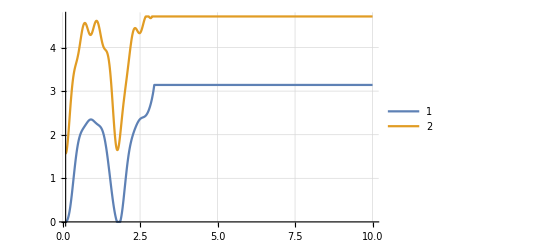

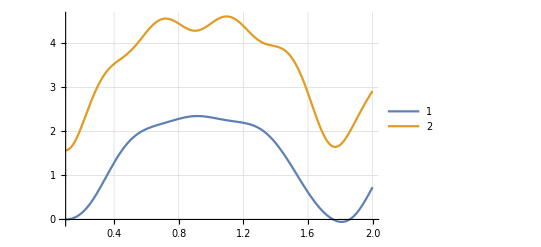

C:/Users/Warsars/Documents/Программирование и проекты/Расчетка Биомеханика/Data/angle_data.xls

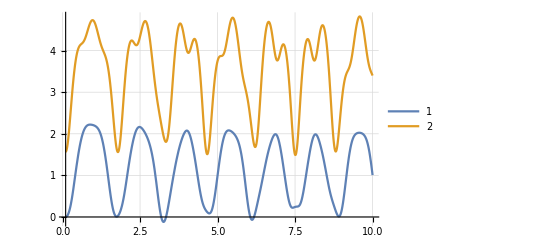

```mathematica
nm=1 ; (*Количество мышц*)
nmp=1;
DataTable=Import["C:/Users/Warsars/Documents/Программирование и проекты/Расчетка Биомеханика/Data/muscles.xls",{"Data",1,Range[2,1+nm],Range[2,24]}] ;(*Импорт данных о мышцах, необходимо указать путь к файлу с данными*)
(*Локоть*)
a=DataTable[[All,1]];
b=DataTable[[All,2]];
c=DataTable[[All,3]];
k=DataTable[[All,4]];
A=DataTable[[All,5]];
B=DataTable[[All,6]];
(*Плечо*)
gl=DataTable[[All,18]];
e=DataTable[[All,19]];
d=DataTable[[All,20]];.13
kl=DataTable[[All,21]];
Al=DataTable[[All,22]];
Bl=DataTable[[All,23]];
g=9.8;
Subscript[α, 0]=DataTable[[1,8]];
Subscript[β, 0]=DataTable[[1,9]];
Subscript[υ, α0]=DataTable[[1,10]];
Subscript[υ, β0]=DataTable[[1,11]];
Subscript[S, 1]=DataTable[[1,12]];
Subscript[S, 2]=DataTable[[1,13]];
Subscript[m, 1]=DataTable[[1,14]];
Subscript[m, 2]=DataTable[[1,15]];
Subscript[m, gr]=DataTable[[1,16]];

(*Доп углы*)
γ=(π/2+β[t])/2;(*Угол связки в локте*)
ϕ=((3π)/2-α[t])/2;
(*Скорости*)
Subscript[ω, 1]=D[α[t],t];
Subscript[ω, 2]=D[β[t],t];
(*Расчет Лагранжа*)
Subscript[i, 1]=Subscript[m, 1] Subscript[S, 1]^2/3;
Subscript[i, 2]=Subscript[m, 2] Subscript[S, 2]^2/3;
Subscript[l, 1]=Sqrt[a^2+c^2-2a*c Cos[γ]];
Subscript[l, 2]=Sqrt[b^2+c^2-2b*c Cos[γ]];
Subscript[f, 1]=Sqrt[gl^2+d^2-2gl*d Cos[ϕ]];
Subscript[f, 2]=Sqrt[e^2+d^2-2e*d Cos[ϕ]];
Δx=Range[1,nm];
Δf=Range[1,nmp];
For[i=1,i<nm+1,i++,Δx[[i]]=((Subscript[l, 1][[i]]+Subscript[l, 2][[i]])-((Subscript[l, 1][[i]]/.γ->π/2)+(Subscript[l, 2][[i]]/.γ->π/2)))];
For[i=1,i<nmp+1,i++,Δf[[i]]=((Subscript[f, 1][[i]]+Subscript[f, 2][[i]])-((Subscript[f, 1][[i]]/.ϕ->(3π)/4)+(Subscript[f, 2][[i]]/.ϕ->(3π)/4)))];

κ=Subscript[i, 1] Subscript[ω, 1]^2/2 + Subscript[i, 2] Subscript[ω, 2]^2/2+(Subscript[ω, 1] Subscript[S, 1])^2 Subscript[m, 2]/2;
Πkl=Sum[k[[i]]*(Δx[[i]])^2/2,{i,1,nm}];
Πkp=Sum[kl[[i]]*(Δf[[i]])^2/2,{i,1,nmp}];

Π=Πk+(Subscript[S, 1]+Subscript[S, 2]-Subscript[S, 1]/2 Cos[α[t]])Subscript[m, 1] g+(Subscript[S, 1]+Subscript[S, 2]-Subscript[S, 1] Cos[α[t]]-Subscript[S, 2]/2 Sin[β[t]-α[t]])Subscript[m, 2] g+(Subscript[S, 1]+Subscript[S, 2]-Subscript[S, 1] Cos[α[t]]-Subscript[S, 2] Sin[β[t]-α[t]])Subscript[m, gr] g;(*Потециальная энергия версия 1*)
(*Π=Πkl+Πkp+(-Subscript[S, 1]/2Cos[α[t]])Subscript[m, 1] g+(-Subscript[S, 1]Cos[α[t]]+Subscript[S, 2]/2 Cos[β[t]+π/2-α[t]])Subscript[m, 2] g+(-Subscript[S, 1]Cos[α[t]]+Subscript[S, 2] Cos[β[t]+π/2-α[t]])Subscript[m, gr] g;*)
υl=D[Subscript[l, 1]+Subscript[l, 2],t];
υp=D[Subscript[f, 1]+Subscript[f, 2],t];
Subscript[F, l]=-Sum[B[[i]]*υl[[i]],{i,1,nm}];
Subscript[F, p]=-Sum[Bl[[i]]*υp[[i]],{i,1,nmp}];
Q=Subscript[F, l]+Subscript[F, p]+Sum[A[[i]],{i,1,nm}]+Sum[Al[[i]],{i,1,nmp}];
genCoords={α[t],β[t]};
eqs=LagrangianEquations[κ,Π,Q,genCoords];
IC={α[0.1]==Subscript[α, 0],β[0.1]==Subscript[β, 0],α'[0.1]==Subscript[υ, α0],β'[0.1]==Subscript[υ, β0]};
sol=NDSolve[Join[eqs,IC],{α[t],β[t]},{t,0.1,10}];
fβ[t]= β[t]/.sol;
fα[t]= α[t]/.sol;
Plot[{Clip[fα[t],{0,π}],Clip[fβ[t],{π/2,3*π/2}]},{t,0.1,10},GridLines->Automatic,PlotLegends->Automatic] 
Plot[{fα[t],fβ[t]},{t,0.1,2},GridLines->Automatic,PlotLegends->Automatic]
Export["C:/Users/Warsars/Documents/Программирование и проекты/Расчетка Биомеханика/Data/angle_data.xls",Table[Flatten[{t,Clip[α[t],{0,π}],Clip[β[t],{π/2,3*π/2}]}/.sol],{t,0.1,10,0.1}]]
```

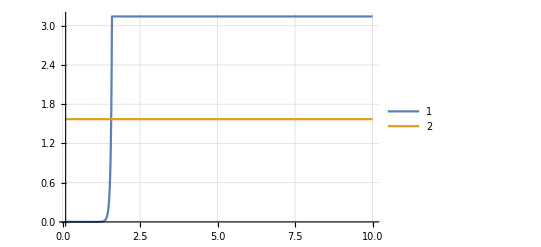

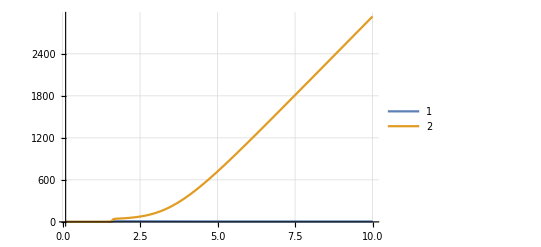

{{α[t]→InterpolatingFunction[{{0.1, 10.}}, <>][t],β[t]→InterpolatingFunction[{{0.1, 10.}}, <>][t]}}

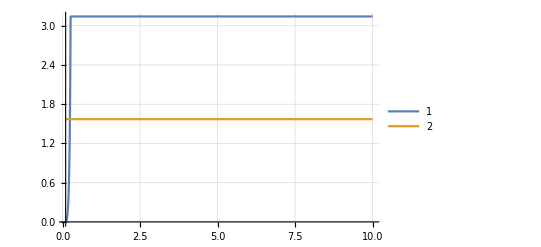

(x')^2

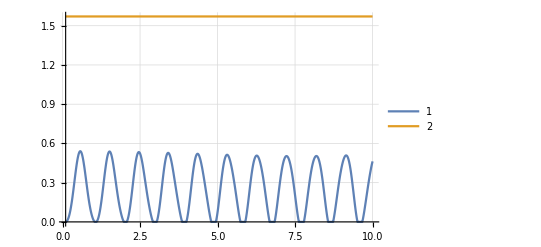

```mathematica
Plot[{Clip[fα[t],{0,π}],Clip[fβ[t],{-π/2,π/2}]},{t,0.1,10},GridLines->Automatic,PlotLegends->Automatic]
```

```mathematica
(Subscript[f, 1]/.ϕ->(3π)/4)+(Subscript[f, 2]/.ϕ->(3π)/4)
```

{0.377893}